```mathematica
Clear["Global`*"];
newtonG = 39.42; (* in AU^3/(M_⊙yr^2) *)
mJupiter = 0.00095492; (* in M_⊙ *)
```

## Calculating the radial velocity profile

The following code snippet calculates the radial velocity profile for a binary system. The function “calcRVunnorm” integrates the equations of motion over a single period, given a choice of eccentricity e and angle between the line of sight and the periapse ϕ. The initial time is set to when the system is at periapse, and distances are in units of the semi-major axis, and times in units of the 
period.

semiAmp calculates the amplitude of the curve from calcRV, given the mass of the observed star m_1, its companion m_2 (masses in M_⊙) , the period in years, and sin i (the inclination angle)

```mathematica
Clear[calcRV, semiAmp];
calcRV[ein_, ϕ_] := 
Module[{soln, vx, vy, vr, twobodyequations,r,e,θ,t, semiAmp},
	twobodyequations = {r''[t] == -4 π^2/r[t]^2 + r[t] θ'[t]^2, 
						θ'[t] == 2π Sqrt[1-e^2] /r[t]^2, 
						θ[0]==0, r[0]==1-e, r'[0]==0};
	soln = NDSolve[twobodyequations/.{e->ein},{r, θ}, {t,0,1}];
	vx[t_] = D[(r[t]Cos[θ[t]])/.soln,t];
	vy[t_] = D[(r[t]Sin[θ[t]])/.soln,t];
	vr[t_] =vx[t] Cos[ϕ] + vy[t] Sin[ϕ];
	vr
];

semiAmp[m1_, m2_, period_, sini_] := 
	4.74372 Sqrt[newtonG]/(2π) m2 sini (m1+m2)^(-2/3) period^(-1/3);
```

```mathematica
semiAmp[1, mJupiter, 1,1]
```

0.00452364

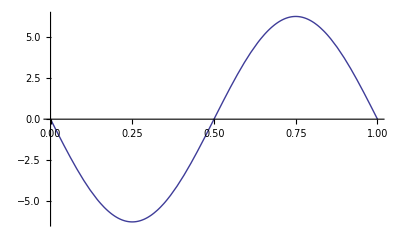

```mathematica
Plot[calcRV[0, 0][t], {t,0,1}]
```

```mathematica
Manipulate[
tmp = calcRV[ein,ϕ];
Plot[tmp[t], {t,0,1}], {ein,0,0.9}, {ϕ,0,2π}]
```